```mathematica
absErrorMthElt[backorbit_,m_,fx_,precision_]:=
Module[{j,k,el,z,,loglinpairs,loglinpair,la,arg,args,nm,aa,xx,b1,m1,bb,zeros,zr,approxr,estimate,fxerror,relerror,relerrors,rellog,relerrmoduli},
zeros=backorbit;
el=Length[zeros];
args={};
loglinpairs={};

k=1;
z=zeros[[k]];
la=Re[Log[Abs[z-fx]]];
arg=Arg[z-fx];
loglinpair={arg,la};
args=Append[args,arg];
loglinpairs=Append[loglinpairs,loglinpair];

For[k=1,k<el,k++;
z=zeros[[k]];
la=Re[Log[Abs[z-fx]]];
arg=Arg[z-fx];
While[Not[arg>Max[args]],arg=arg+2*Pi];
args=Append[args,arg];
loglinpair={arg,la};
loglinpairs=Append[loglinpairs,loglinpair]];

outargs=args;
outpairs=loglinpairs;
nm=FindFit[loglinpairs,aa*xx+bb,{aa,bb},{xx},PrecisionGoal->precision];
m1=nm[[1,2]];
b1=nm[[2,2]];

relerrors={};
relerrmoduli={};
j=m;
zr=zeros[[j]];
arg=args[[j]];
approxr=Exp[m1*arg+b1];
estimate=approxr*(Cos[arg]+I*Sin[arg]);
fxerror=zr-fx-estimate;
abserror=Abs[fxerror];

Return[abserror]]
```

```mathematica
absErrorMthElt2[backorbit_,m_,fx_,precision_]:=
Module[{j,k,el,z,,loglinpairs,loglinpair,la,arg,args,nm,aa,xx,b1,m1,bb,zeros,zr,approxr,estimate,fxerror,relerror,relerrors,rellog,relerrmoduli},
zeros=backorbit;
el=Length[zeros];
args={};
loglinpairs={};

(* omit k = 1 *)
For[k=1,k<el,k++;
z=zeros[[k]];
la=Re[Log[Abs[z-fx]]];
arg=Arg[z-fx];
While[Not[arg>Max[args]],arg=arg+2*Pi];
args=Append[args,arg];
loglinpair={arg,la};
loglinpairs=Append[loglinpairs,loglinpair]];

outargs=args;
outpairs=loglinpairs;
nm=FindFit[loglinpairs,aa*xx+bb,{aa,bb},{xx},PrecisionGoal->precision];
m1=nm[[1,2]];
b1=nm[[2,2]];

relerrors={};
relerrmoduli={};
j=m;
zr=zeros[[j]];
arg=args[[j]];
approxr=Exp[m1*arg+b1];
estimate=approxr*(Cos[arg]+I*Sin[arg]);
fxerror=zr-fx-estimate;
abserror=Abs[fxerror];

Return[abserror]]
```

```mathematica
absErrorMthElt3[backorbit_,fx_,precision_]:=
Module[{j,k,el,z,,pairs,pair,la,arg,args,nm,aa,xx,b1,m1,bb,zeros,zr,approxr,estimate,fxerror,relerror,relerrors,rellog,relerrmoduli,rlrho,imrho,imapproxrho},
zeros=backorbit;
el=Length[backorbit];

pairs={};

(* omit k = 1 *)
For[k=1,k<el,k++;
z=backorbit[[k]];

pair={Re[z],Im[z]};
pairs=Append[pairs,pair]];


nm=FindFit[pairs,aa*xx+bb,{aa,bb},{xx},PrecisionGoal->precision];
m1=nm[[1,2]];
b1=nm[[2,2]];


rlrho=Re[backorbit[[1]]];
imapproxrho=m1*rlrho+b1;
estimate=rlrho+imapproxrho*I;
fxerror=backorbit[[1]]-estimate;
abserror=Abs[fxerror];

Return[abserror]]
```

```mathematica
stream=OpenRead["realfxpts24may16no11"];
ls=ReadList[stream];
Close[stream]
```

realfxpts24may16no11

```mathematica
stream=OpenRead["realfxpts24may16no11"];
ls=ReadList[stream];
Close[stream];
stream1=OpenRead["realfxNrhoNrun31may16no6 copy"];
list=ReadList[stream1];
Close[stream1];
precision=500;
data={};
m=1;
For[n=0,n<1,n++;

backorbit={};
fx=ls[[n,2]];

For[a=0,j=a<Length[list],a++;

If[
list[[a,1]]==n,backorbit=
Append[
backorbit,list[[a,3]]
] (* close Append  *)

] (*close If loop  *)

]; (*close a loop *)
Print["length backorbit  ",Length[backorbit]];
datum = absErrorMthElt [backorbit,m,fx,precision];
Print[n];
Print[datum]
] ;(* close n loop *)
```

length backorbit  100

1

70.571773254960712443019638856678558185167286487539195620336851479003089171338569608477396533903260365802354021128089991235782851191956386545824648670498097604099379251792565843064627091311332148248149974218846110670460731386605665102909571119780824243881455297830268588298981398597258175826543248958882755881395727528078150565916035170178132569093617923297969435920824623124

```mathematica
stream=OpenRead["realfxpts24may16no11"];
ls=ReadList[stream];
Close[stream];Print["length  ",Length[ls]]
```

length  241

```mathematica
ls[[241]]
```

{-500,-500.000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000001008151136224289947516897113387688847184939530141536883886302983975224297720599637246346172066607183789938601538015339326285793726534473279806079073050006446708872644163603712076323852755660156913964016369818443878640061482260452833666266985291940516523001907962582}

```mathematica
stream1=OpenRead["realfxNrhoNrun31may16no5 copy"];
list=ReadList[stream1];
Close[stream1];
Length[list]
```

2500

```mathematica
list[[1]]
```

{1,1,1/2+14.13472514173469379045725198356247027078425711569924317568556746014996342980925676494901039317156101277920297154879743676614269146988225458250536323944713778041338123720597054962195586586020055556672583601077370020541098266150754278051744259130625448197865107230493872562973832157742039521572567480933214003499046803434626731442092037738548714137831735639699536542811307968053149168852906782082298049264338666734623320078758761792005604868054356801444424651065597568665903228686510544859444320624072727032094274522213048748720924123851418351460542790152447833835425453344004487936806761697300819000731393854983736215013045167269683892003917628512321285422052396913342583227533516406016976352756375896953767492033612720925999173042707568308795118445348918008630082648312516911271068291052375961797743181517071354531677549515382893784903647470972701994848553220925357435790922612524773659551801697523346121397731600535412592674745572587780147260983080897860071253208750939599796666067537838121489190886 ⅈ}

```mathematica
Last[list]
```

{50,50,-117.99999999999999999999999999999999999999999999999999999999999999999999999999999999999999999999999999228260322118000322353734247500523741008442158932621943547952848608038688173670028970907546131063951447164113920117684995315673559479194951136683002415715230307460168070452232957524438720994716230229928331939852190118212155811447013057987810002710798907881157151393669499131578256193258025267490673510591620376815618849492074544472744548105616155716139477146829213474138546922218386965599497282858362419532871969600220051941575334312929580174159724811411913650127477850380957308109495572250832749851}

absolute error

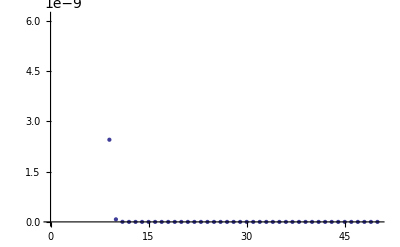

log absolute error

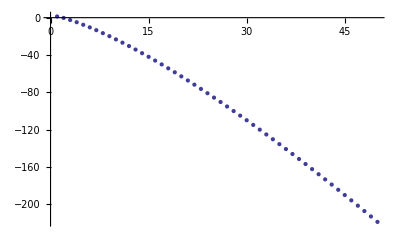

running mean absolute error

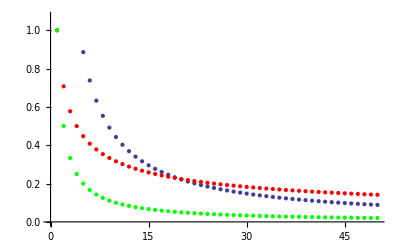

```mathematica
stream=OpenRead["realfxpts24may16no11"];
ls=ReadList[stream];
Close[stream];
stream1=OpenRead["realfxNrhoNrun31may16no5 copy"];
list=ReadList[stream1];
Close[stream1];
precision=500;
data={};
logdata={};
meandata={};
redcurve={};
greencurve={};
m=1;
For[n=0,n<50,n++;

backorbit={};
fx=ls[[n,2]];

For[a=0,j=a<Length[list],a++;

If[
list[[a,1]]==n,backorbit=
Append[
backorbit,list[[a,3]]
] (* close Append  *)

] (*close If loop  *)

]; (*close a loop *)


datum = absErrorMthElt3[backorbit,fx,precision];
data=Append[data,datum];
meandata=Append[meandata,Mean[data]];
redcurve=Append[redcurve,1/n^.5];
greencurve=Append[greencurve,1/n^1];
logmeandata=Append[logmeandata,Log[Mean[data]]];
logdata=Append[logdata,Log[datum]]
] (* close n loop *);
Print["absolute error"];
Print[ListPlot[data]];
Print["log absolute error"];
Print[ListPlot[logdata]];
Print["running mean absolute error"];
Print[Show[ListPlot[meandata],ListPlot[redcurve,PlotStyle->Red],ListPlot[greencurve,PlotStyle->Green]]]
```

absolute error

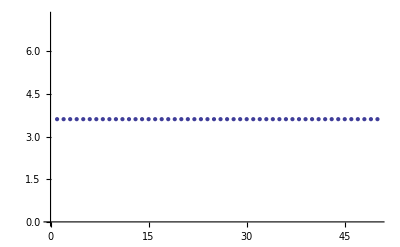

log absolute error

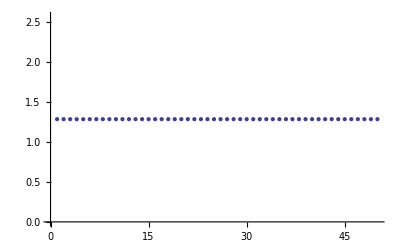

running mean absolute error

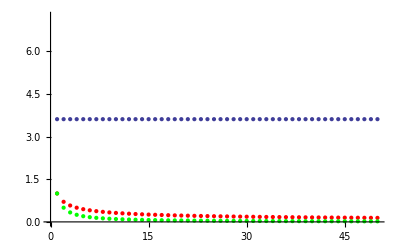

```mathematica
stream=OpenRead["realfxpts24may16no11"];
ls=ReadList[stream];
Close[stream];
stream1=OpenRead["realfxNrhoNrun31may16no5 copy"];
list=ReadList[stream1];
Close[stream1];
precision=500;
data={};
logdata={};
meandata={};
redcurve={};
greencurve={};
m=1;
For[n=0,n<50,n++;

backorbit={};
fx=ls[[n,2]];

For[a=0,j=a<Length[list],a++;

If[
list[[a,1]]==1,backorbit=
Append[
backorbit,list[[a,3]]
] (* close Append  *)

] (*close If loop  *)

]; (*close a loop *)


datum = absErrorMthElt3[backorbit,fx,precision];
data=Append[data,datum];
meandata=Append[meandata,Mean[data]];
redcurve=Append[redcurve,1/n^.5];
greencurve=Append[greencurve,1/n^1];
logmeandata=Append[logmeandata,Log[Mean[data]]];
logdata=Append[logdata,Log[datum]]
] (* close n loop *);
Print["absolute error"];
Print[ListPlot[data]];
Print["log absolute error"];
Print[ListPlot[logdata]];
Print["running mean absolute error"];
Print[Show[ListPlot[meandata],ListPlot[redcurve,PlotStyle->Red],ListPlot[greencurve,PlotStyle->Green]]]
```

```mathematica
stream=OpenRead["realfxpts24may16no11"];
ls=ReadList[stream];
Close[stream];
stream1=OpenRead["realfxNrhoNrun31may16no5 copy"];
list=ReadList[stream1];
Close[stream1];
precision=500;
data={};
logdata={};
meandata={};
redcurve={};
greencurve={};
m=1;
For[n=0,n<50,n++;

backorbit={};
fx=ls[[n,2]];

For[a=0,j=a<Length[list],a++;

If[
list[[a,1]]==n,backorbit=
Append[
backorbit,list[[a,3]]
] (* close Append  *)

] (*close If loop  *)

]; (*close a loop *)


datum = absErrorMthElt3[backorbit,fx,precision];
data=Append[data,datum];

redcurve=Append[redcurve,-n^(1.4)];
greencurve=Append[greencurve,-n^(1.35)];

logdata=Append[logdata,Log[datum]]
] (* close n loop *);
Print["absolute error"];
Print[ListPlot[data]];
Print["log absolute error"];
Print[Show[ListPlot[logdata,PlotStyle->Blue],ListPlot[greencurve,PlotStyle->Green],ListPlot[redcurve,PlotStyle->Red]]]
```

absolute error

-Graphics-

### leaf6point8left

log absolute error

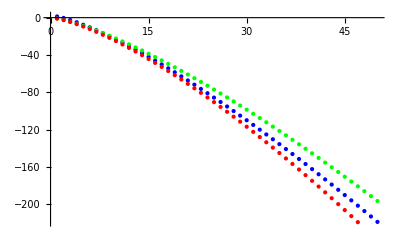

&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&

n  1

fixed point ~ -20.1312

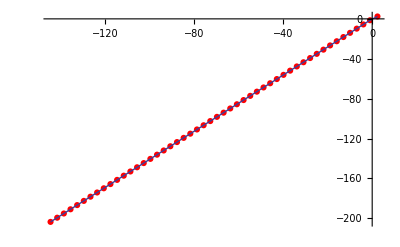

&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&

n  2

fixed point ~ -21.9855

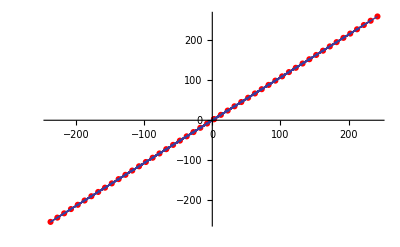

&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&

n  3

fixed point ~ -24.0011

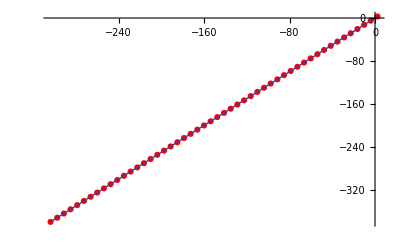

&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&

n  4

fixed point ~ -25.9999

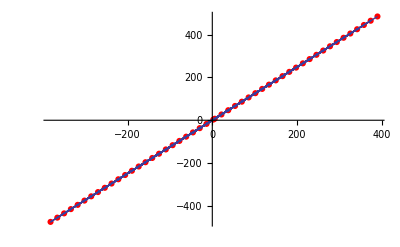

&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&

n  5

fixed point ~ -28.

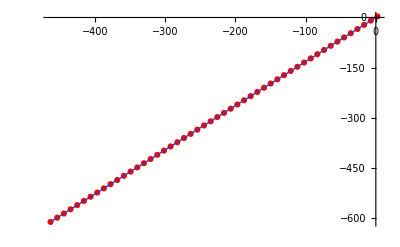

&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&

n  6

fixed point ~ -30.

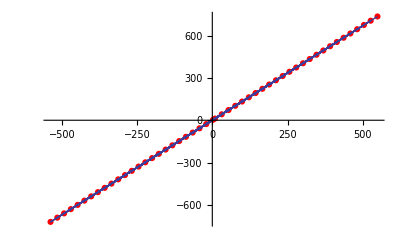

&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&

n  7

fixed point ~ -32.

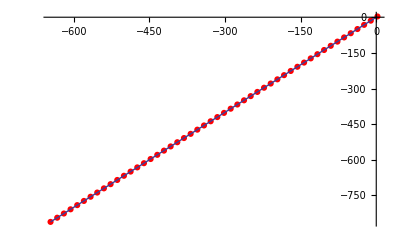

&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&

n  8

fixed point ~ -34.

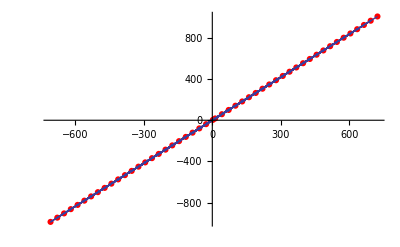

&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&

n  9

fixed point ~ -36.

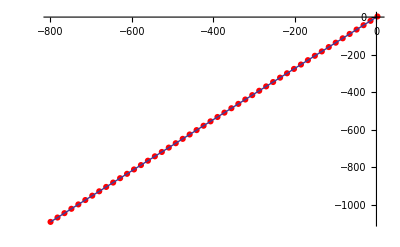

&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&

n  10

fixed point ~ -38.

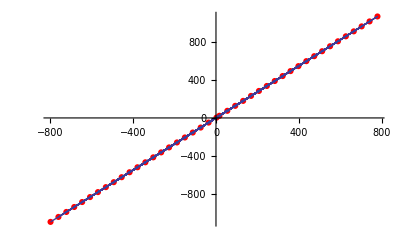

&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&

n  11

fixed point ~ -40.

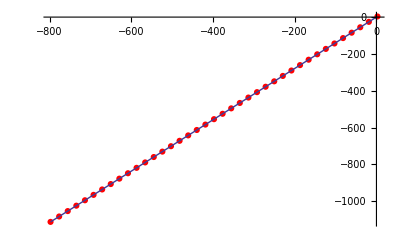

&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&

n  12

fixed point ~ -42.

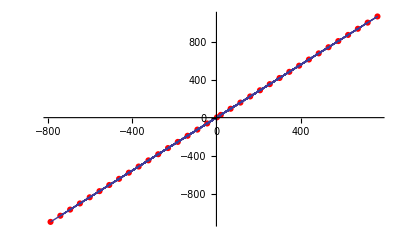

&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&

n  13

fixed point ~ -44.

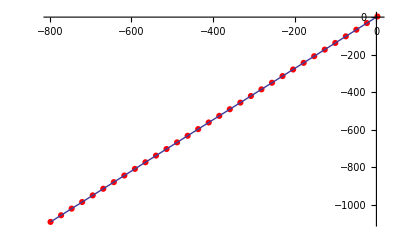

&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&

n  14

fixed point ~ -46.

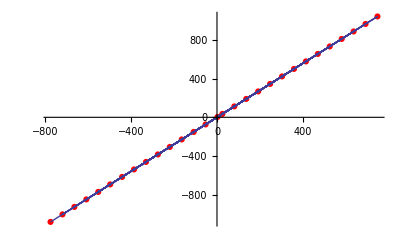

&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&

n  15

fixed point ~ -48.

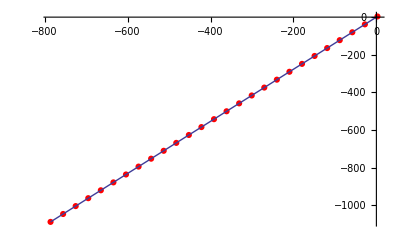

&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&

n  16

fixed point ~ -50.

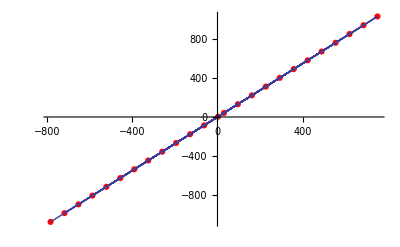

&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&

n  17

fixed point ~ -52.

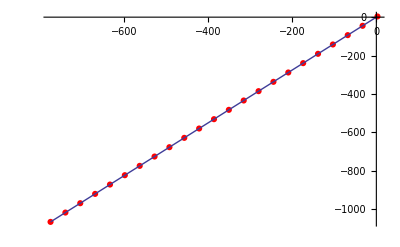

&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&

n  18

fixed point ~ -54.

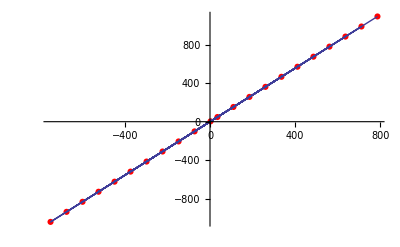

&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&

n  19

fixed point ~ -56.

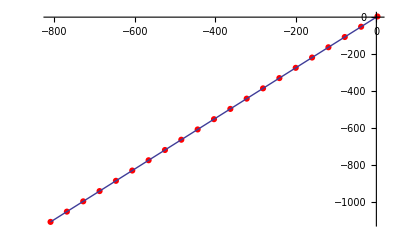

&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&

n  20

fixed point ~ -58.

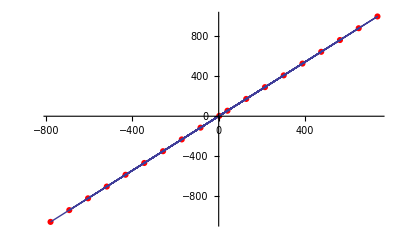

&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&

n  21

fixed point ~ -60.

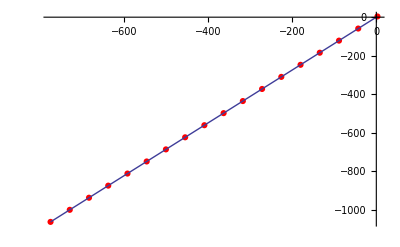

&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&

n  22

fixed point ~ -62.

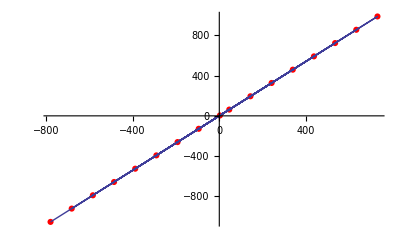

&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&

n  23

fixed point ~ -64.

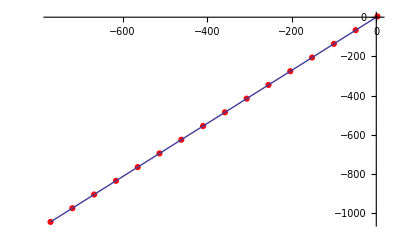

&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&

n  24

fixed point ~ -66.

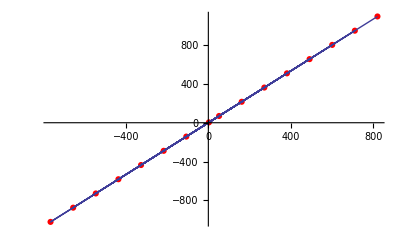

&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&

n  25

fixed point ~ -68.

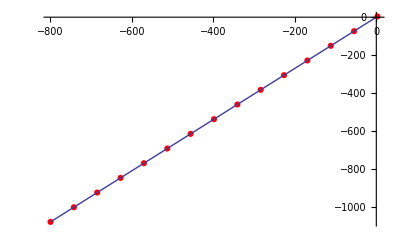

&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&

n  26

fixed point ~ -70.

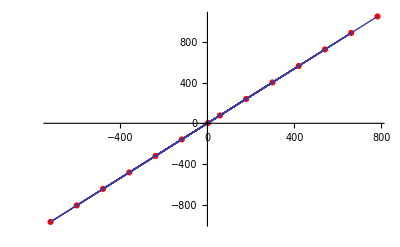

&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&

n  27

fixed point ~ -72.

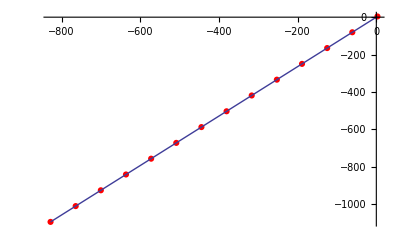

&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&

n  28

fixed point ~ -74.

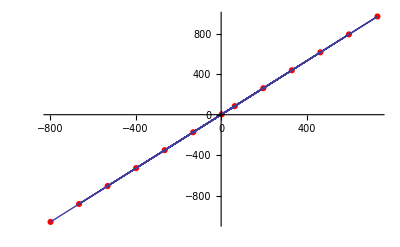

&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&

n  29

fixed point ~ -76.

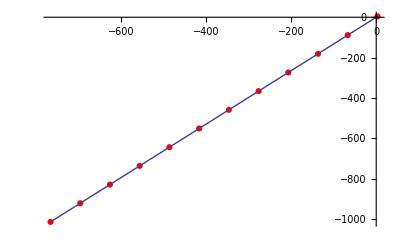

&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&

n  30

fixed point ~ -78.

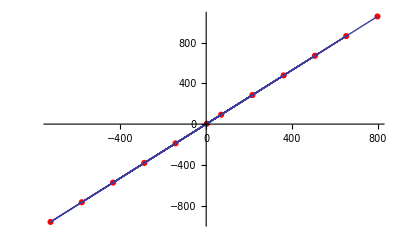

&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&

n  31

fixed point ~ -80.

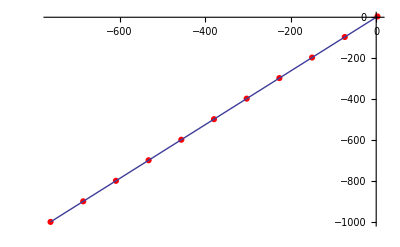

&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&

n  32

fixed point ~ -82.

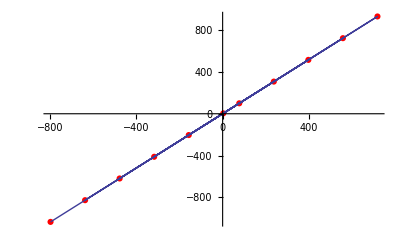

&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&

n  33

fixed point ~ -84.

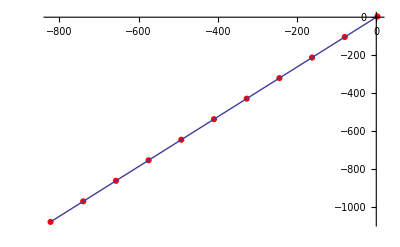

&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&

n  34

fixed point ~ -86.

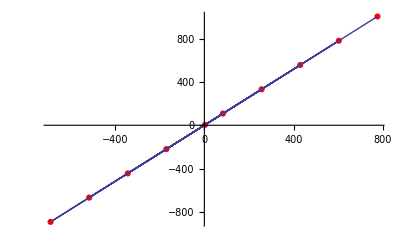

&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&

n  35

fixed point ~ -88.

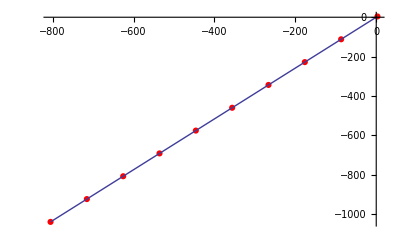

&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&

n  36

fixed point ~ -90.

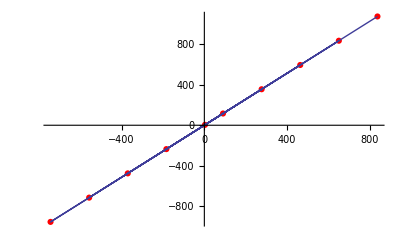

&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&

n  37

fixed point ~ -92.

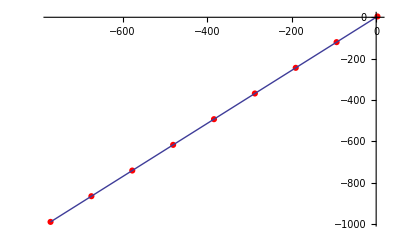

&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&

n  38

fixed point ~ -94.

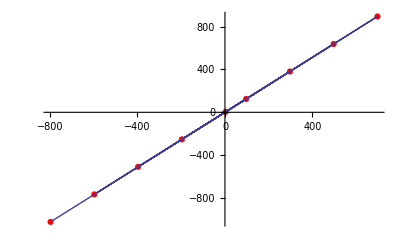

&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&

n  39

fixed point ~ -96.

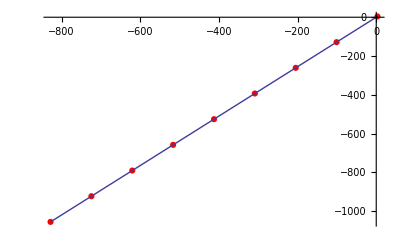

&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&

n  40

fixed point ~ -98.

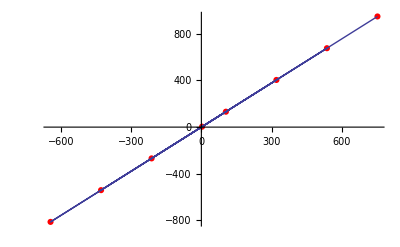

&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&

n  41

fixed point ~ -100.

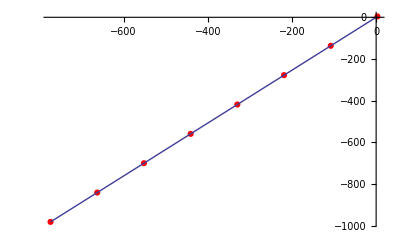

&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&

n  42

fixed point ~ -102.

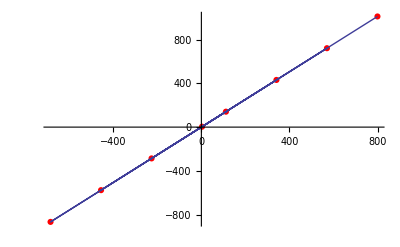

&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&

n  43

fixed point ~ -104.

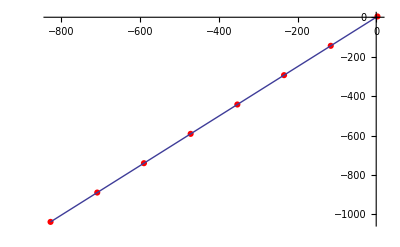

&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&

n  44

fixed point ~ -106.

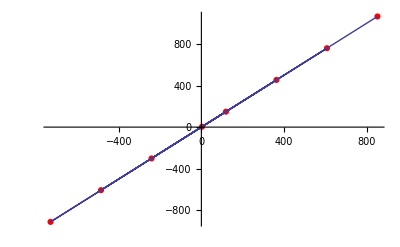

&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&

n  45

fixed point ~ -108.

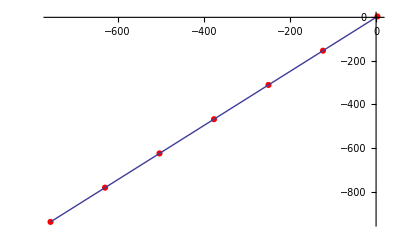

&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&

n  46

fixed point ~ -110.

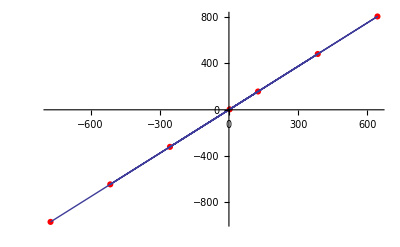

&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&

n  47

fixed point ~ -112.

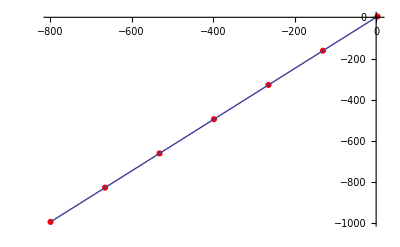

&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&

n  48

fixed point ~ -114.

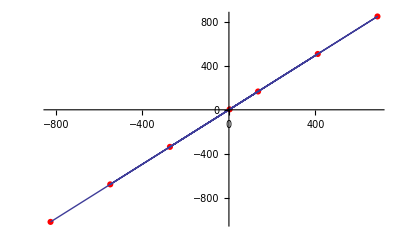

&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&

n  49

fixed point ~ -116.

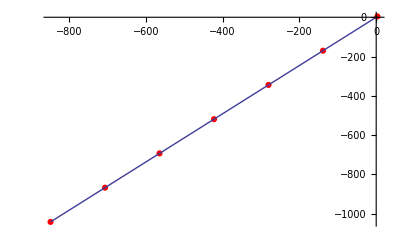

&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&

n  50

fixed point ~ -118.

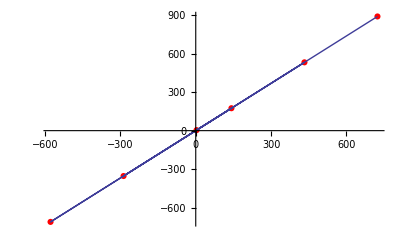

elasped seconds   1874.88819

```mathematica
start=SessionTime[];
streamzeros=OpenRead["betterbarryzeros"];
betterbarryzeroslist=ReadList[streamzeros];
Close[streamzeros];
streamfx=OpenRead["realfxpts24may16no11"];
fxlist=ReadList[streamfx];
Close[streamfx];

stream1=OpenWrite["realfxNrhoN+1run25mar17"];
precision=500;
For[n=0,n<50,n++;
orbit={};
shortorbit={};
data={};
orbitpairs={};
args={};
thetaset={};
errorpairs={};
relerrorpairs={};
targetzero=1/2+I*Im[betterbarryzeroslist[[n+1]]];
fx=N[fxlist[[n,2]],1000];
Print["&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&"];
Print["n  ",n];
Print["fixed point ~ ",N[Round[fx,1/10^10]]];

k=1;
zr=targetzero;
Write[stream1,{n,k,zr}];
orbit=Append[orbit,zr];
arg=Arg[zr-fx];
args=Append[args,arg];
la=Re[Log[Abs[zr-fx]]];
orbitpair={la*Cos[arg],la*Sin[arg]};
orbitpairs=Append[orbitpairs,orbitpair];


For[k=1,k<50,k++;
startcenter=fx;
x=orbit[[k-1]];
zr=FindRoot[zetaIterate[s,1]-x,{s,startcenter},PrecisionGoal->precision+50,WorkingPrecision->precision+100][[1,2]];
Write[stream1,{n,k,zr}];
orbit=Append[orbit,zr];
shortorbit=Append[shortorbit,zr];
arg=Arg[zr-fx];
While[Not[arg-Last[args]>1],arg=arg+2*Pi];
args=Append[args,arg];
la=Re[Log[Abs[zr-fx]]];
orbitpair={la*Cos[arg],la*Sin[arg]};
orbitpairs=Append[orbitpairs,orbitpair]
](*close k loop *)

Print[Show[ListPlot[orbitpairs,PlotStyle->{Red,PointSize[.011]}],ListPlot[orbitpairs,Joined->True]]];
];(* close n-loop *)
Close[stream1];
Print["elasped seconds   ",SessionTime[]-start]
```

absolute error

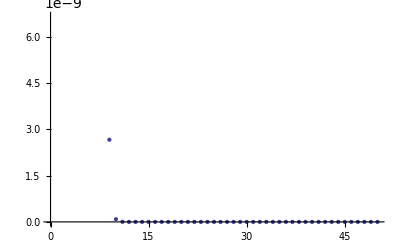

```mathematica
stream=OpenRead["realfxpts24may16no11"];
ls=ReadList[stream];
Close[stream];
stream1=OpenRead["realfxNrhoN+1run25mar17"];
list=ReadList[stream1];
Close[stream1];
precision=500;
data={};
logdata={};
meandata={};
redcurve={};
greencurve={};
m=1;
For[n=0,n<50,n++;

backorbit={};
fx=ls[[n,2]];

For[a=0,j=a<Length[list],a++;

If[
list[[a,1]]==n,backorbit=
Append[
backorbit,list[[a,3]]
] (* close Append  *)

] (*close If loop  *)

]; (*close a loop *)


datum = absErrorMthElt3[backorbit,fx,precision];
data=Append[data,datum];

redcurve=Append[redcurve,-n^(1.4)];
greencurve=Append[greencurve,-n^(1.35)];

logdata=Append[logdata,Log[datum]]
] (* close n loop *);
Print["absolute error"];
Print[ListPlot[data]];
Print["log absolute error"];
Print[Show[ListPlot[logdata,PlotStyle->Blue],ListPlot[greencurve,PlotStyle->Green],ListPlot[redcurve,PlotStyle->Red]]]
```

### leaf6point8right

log absolute error